```mathematica
τ=.
ρ=.
a=.
b=.
PL=.

ρ[τ_]=v*(1-Exp[-τ/tr])
Pisi=ρ[t] Exp[-Integrate[ρ[τ],{τ,0,t}]]/.{tr->100,v->2}
PL:=NIntegrate[Pisi Exp[-(a+I b) t],{t,0,Infinity}]
```

(1-ⅇ^(-τ/tr)) v

2 ⅇ^(-2 (100 (-1+ⅇ^(-t/100))+t)) (1-ⅇ^(-t/100))

```mathematica
Plot3D[Re[PL],{a,-1,0},{b,-2,2}]
Plot3D[Im[PL],{a,-1,0},{b,-2,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {76.1924}. NIntegrate obtained 0.178833-0.0219727 ⅈ and 1.76784 for the integral and error estimates.

-Graphics3D-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {76.1924}. NIntegrate obtained 0.178833-0.0219727 ⅈ and 1.76784 for the integral and error estimates.

-Graphics3D-

NIntegrate::inumr: The integrand 2 ⅇ^((-a-ⅈ b) t-2 (100 (-1+Power[«2»])+t)) (1-ⅇ^(-t/100)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {71.9803}. NIntegrate obtained 0.0986328+0.0500488 ⅈ and 1.77516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {71.9803}. NIntegrate obtained 0.0986328+0.0500488 ⅈ and 1.77516 for the integral and error estimates.

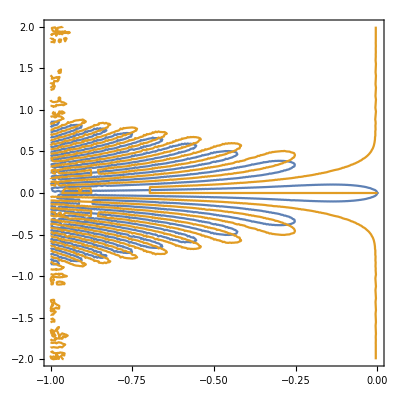

```mathematica
ContourPlot[{Re[PL]==1,Im[PL]==0},{a,-1,0},{b,-2,2}]
```